```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/baryon_number_fluc/phasedata

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,0,800,50}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,0,800,50}];
r42=chi4/chi2;
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

```mathematica
r42[[1;;5]][[1;;60]]=1;
r42[[6;;10]][[1;;50]]=1;
r42[[11;;12]][[1;;40]]=1;
r42[[13;;14]][[1;;30]]=1;
r42[[15;;17]][[1;;15]]=1;
```

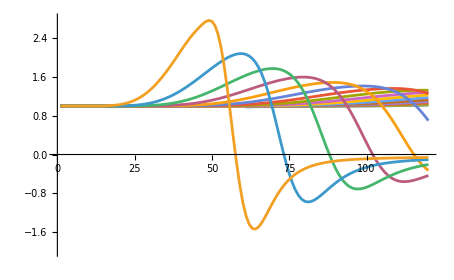

```mathematica
ListLinePlot[r42,PlotRange->{All,{-2,2.8}}]
```

```mathematica
ListDensityPlot[Transpose[r42],PlotRange->{All,All,{-1.8,2.8}}]
```

-Graphics-